# Типовой Расчёт Вариант 4 Крюк В.В. 221703

```mathematica
data=({{-0.5, 0.419945}, {-0.412, 0.395988}, {-0.324, 0.391402}, {-0.236, 0.374437}, {-0.148, 0.375642}, {-0.06, 0.364857}, {0.028, 0.371704}, {0.116, 0.366656}, {0.204, 0.379343}, {0.292, 0.379948}, {0.38, 0.399032}, {0.468, 0.405545}, {0.556, 0.43196}, {0.644, 0.444969}, {0.732, 0.480039}, {0.82, 0.500438}, {0.908, 0.545871}, {0.996, 0.574811}, {1.084, 0.632645}, {1.172, 0.67142}, {1.26, 0.743887}, {1.348, 0.793733}, {1.436, 0.882993}, {1.524, 0.944755}, {1.612, 1.05247}, {1.7, 1.12614}});
a = -0.5;
b = 1.7;
h = 0.088;
dots = (b-a)/h+1;
dataTable = Table[{data[[i,1]],data[[i,2]]}, {i,1,dots}]
```

{{-0.5,0.419945},{-0.412,0.395988},{-0.324,0.391402},{-0.236,0.374437},{-0.148,0.375642},{-0.06,0.364857},{0.028,0.371704},{0.116,0.366656},{0.204,0.379343},{0.292,0.379948},{0.38,0.399032},{0.468,0.405545},{0.556,0.43196},{0.644,0.444969},{0.732,0.480039},{0.82,0.500438},{0.908,0.545871},{0.996,0.574811},{1.084,0.632645},{1.172,0.67142},{1.26,0.743887},{1.348,0.793733},{1.436,0.882993},{1.524,0.944755},{1.612,1.05247},{1.7,1.12614}}

```mathematica
(*График заданной функции*)
```

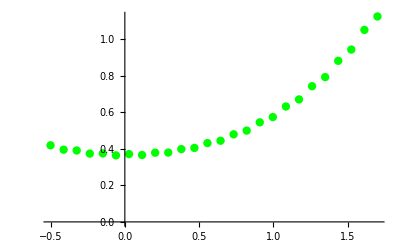

```mathematica
dotsPlot=ListPlot[data,PlotStyle->{PointSize[0.015],Green}];
Show[dotsPlot]
```

## Задание 1.

#### Постройте для функции f(x) интерполяционный многочлен степени n=25 и многочлены меньшей степени на отрезке, используя не все узлы сетки: - используете значения функции в нечетных узлах (n=12); - используете значения функции в каждом 3- узле (n=8); - используете значения функции в каждом 5- узле (n=5). Выведите графики интерполяционных многочленов и оцените их поведение на отрезке. Сравните результаты и сделайте выводы о зависимость погрешности интерполирования от числа узлов.

```mathematica
(*Построение многочлена степенью 25:*)
```

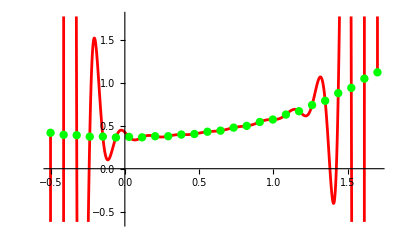

```mathematica
Polynomial25 = InterpolatingPolynomial[dataTable, x];
plot25 = Plot[Polynomial25, {x,a,b}, PlotStyle->{Red}];
dots25=ListPlot[dataTable, PlotStyle->{PointSize[0.015],Green}];Show[plot25,dots25]
```

```mathematica
(*Найдём абсолютную погрешность многочлена в заданных точках*)
```

```mathematica
Diff25 = 
Table[{data[[i,1]], (Polynomial25 /. x-> data[[i,1]])- data[[i,2]]}, {i,1,dots}];
```

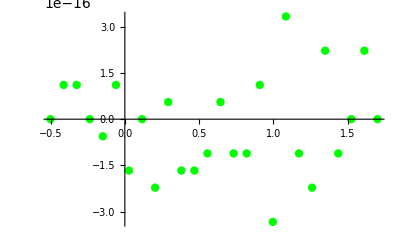

```mathematica
Show[ListPlot[Diff25, PlotStyle->{PointSize[0.015],Green}]]
```

```mathematica
Sum[((Polynomial25/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

6.22461×10^-31

```mathematica
(*Используя значения функции в нечетных узлах:*)
```

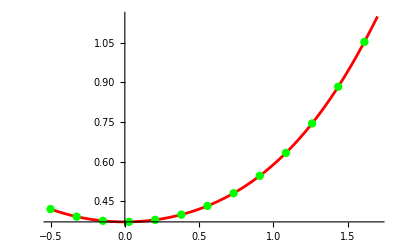

```mathematica
data12 = Table[{data[[i,1]],data[[i,2]]},{i,1,25,2}];
Polynomial12 = InterpolatingPolynomial[data12, x];
plot12 = Plot[Polynomial12, {x,a,b}, PlotStyle->{Red}];
dots12=ListPlot[data12, PlotStyle->{PointSize[0.015],Green}];Show[plot12,dots12]
```

```mathematica
(*Найдём абсолютную погрешность многочлена в заданных точках*)
```

```mathematica
Diff12 = Table[{data[[i,1]], (Polynomial12 /. x-> data[[i,1]])- data[[i,2]]}, {i,1,dots}];
```

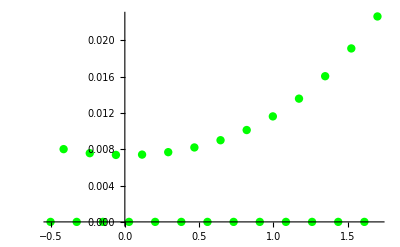

```mathematica
Show[ListPlot[Diff12, PlotStyle->{PointSize[0.015],Green}]]
```

```mathematica
Sum[((Polynomial12/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

0.00199129

```mathematica
(*Используя значения функции в каждом третьем узле:*)
```

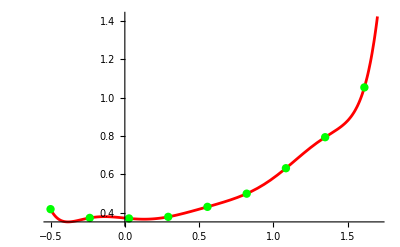

```mathematica
data8 = Table[{data[[i,1]],data[[i,2]]},{i,1,25,3}];
Polynomial8 = InterpolatingPolynomial[data8, x];
plot8 = Plot[Polynomial8, {x,a,b}, PlotStyle->{Red}];
dots8=ListPlot[data8, PlotStyle->{PointSize[0.015],Green}];Show[plot8,dots8]
```

```mathematica
(*Найдём абсолютную погрешность многочлена в заданных точках*)
```

```mathematica
Diff8 = Table[{data[[i,1]], (Polynomial8 /. x-> data[[i,1]])- data[[i,2]]}, {i,1,dots}];
```

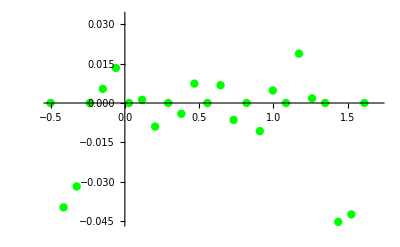

```mathematica
Show[ListPlot[Diff8, PlotStyle->{PointSize[0.015],Green}]]
```

```mathematica
Sum[((Polynomial8/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

0.0942995

```mathematica
(*Используя значения функции в каждом пятом узле:*)
```

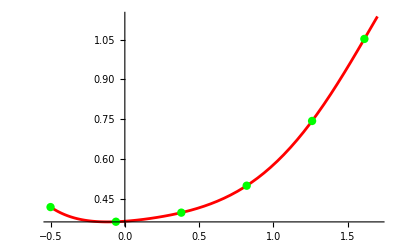

```mathematica
ind = {1,6,11,16,21,25};
data5 = Table[{data[[ind[[i]],1]],data[[ind[[i]],2]]},{i,1,6}];
Polynomial5 = InterpolatingPolynomial[data5, x];
plot5 = Plot[Polynomial5, {x,a,b},PlotStyle->{Red}];
dots5=ListPlot[data5, PlotStyle->{PointSize[0.015],Green}];Show[plot5,dots5]
```

```mathematica
(*Найдём абсолютную погрешность многочлена в заданных точках*)
```

```mathematica
Diff5 = Table[{data[[i,1]], (Polynomial5 /. x-> data[[i,1]])- data[[i,2]]}, {i,1,dots}];
```

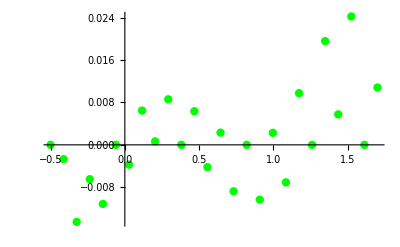

```mathematica
Show[ListPlot[Diff5, PlotStyle->{PointSize[0.015],Green}]]
```

```mathematica
Sum[((Polynomial5/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

0.002037

#### Вывод: наилучшим в сравнении по сумме квадратов разностей функции в заданных узлах оказался многочлен 25-й степени. По графикам можно заметить, что погрешность увеличивается ближе к крайним значениям интерполируемой функции. Но несмотря на это, интерполяция не гарантирует, что поведение полученной функции между узлами интерполяции будет повторять поведение исходной функции (погрешность увеличивается в узлах, которые не были выбраны для интерполяции 5, 8 и 12 степеней).

## Задание 2

#### Постройте сплайны, аппроксимирующие функцию f(x) по значениям в узлах, выведите графики и сравните с графиками интерполяционных многочленов степени n = 5, 8, 12, 25, построенных по тем же узлам.

```mathematica
(*Построим аппроксимирующий сплайн заданного многочлена 5 степени*)
```

```mathematica
Spline5:=Interpolation[data5,x,Method->"Spline"]
SplinePlot5 = Plot[Spline5, {x,a,b}, PlotStyle->{Red}];
```

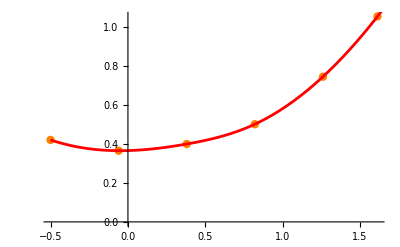

```mathematica
Show[ListPlot[data5, PlotStyle->{PointSize[0.015],Orange}],SplinePlot5]
```

```mathematica
Sum[((Spline5/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

0.00179072

```mathematica
(*Построим аппроксимирующий сплайн заданного многочлена 8 степени*)
```

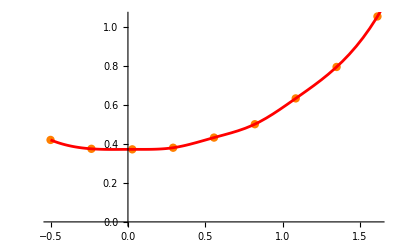

```mathematica
Spline8:=Interpolation[data8,x,Method->"Spline"]
SplinePlot8 = Plot[Spline8, {x,a,b}, PlotStyle->{Red}];
Show[ListPlot[data8, PlotStyle->{PointSize[0.015],Orange}],SplinePlot8]
```

```mathematica
Sum[((Spline8/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

0.00382718

```mathematica
(*Построим аппроксимирующий сплайн заданного многочлена 12 степени*)
```

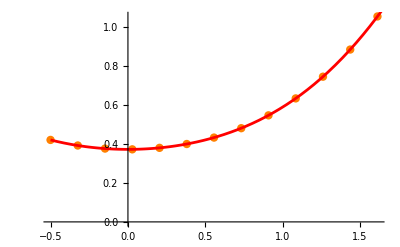

```mathematica
Spline12:=Interpolation[data12,x,Method->"Spline"]
SplinePlot12 = Plot[Spline12, {x,a,b}, PlotStyle->{Red}];
Show[ListPlot[data12, PlotStyle->{PointSize[0.015],Orange}],SplinePlot12]
```

```mathematica
Sum[((Spline12/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

0.00201531

```mathematica
(*Построим аппроксимирующий сплайн заданного многочлена 25 степени*)
```

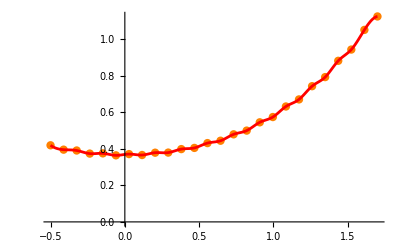

```mathematica
Spline25:=Interpolation[data,x,Method->"Spline"]
SplinePlot25 = Plot[Spline25, {x,a,b}, PlotStyle->{Red}];
Show[ListPlot[data, PlotStyle->{PointSize[0.015],Orange}],SplinePlot25]
```

```mathematica
Sum[((Spline25/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

1.20178×10^-31

#### Вывод: наилучшим в сравнении по сумме квадратов разностей функции в заданных узлах оказался сплайн 25ой степени . Погрешность оказалась меньше, чем в случае интерполяционного многочлена из Задания 1.

## Задание 3

#### Постройте для функции f(x) многочлены наилучшего cреднеквадратичного приближения Pn*(x) степени n = 1,2. Вычислите для каждого многочлена сумму квадратов отклонения в узлах, сравните их значения и сделайте выводы. Выведите графики узлов и многочленов Pn*(x), аппроксимирующих функцию.

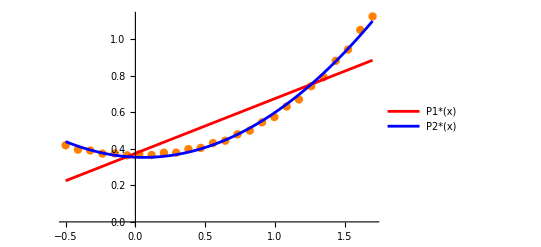

```mathematica
P1=Fit[data,{1,x},x];
P2=Fit[data,{1,x, x^2},x];
PPlot = Plot[{P1,P2}, {x,a,b},PlotStyle->{Red, Blue}, PlotLegends->{"P1*(x)","P2*(x)"}];
Show[ListPlot[data, PlotStyle->{PointSize[0.015],Orange}],PPlot]
```

```mathematica
Sum[((P1/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

0.308321

```mathematica
Sum[((P2/.x->data[[i,1]])-data[[i,2]])^2, {i,dots}]
```

0.00603807

#### Вывод: многочлен наилучшего cреднеквадратичного приближения второго порядка показал лучшую точность графически и исходя из высчитанной суммы квадратов разностей.й

## Задание 4

#### Вычислите определенный интеграл следующими методами : -методами левых, правых и средних прямоугольников; -методом трапеций; -методом парабол (Симпсона). Сравните полученные приближенные значения интеграла и сделайте выводы о точности результата.

```mathematica
(*Метод левых прямоугольников*)
```

```mathematica
LeftRectangle=h*∑_(i=1)^(dots-1) data[[i,2]]
```

1.17256

```mathematica
(*Метод правых прямоугольников*)
```

```mathematica
RightRectangle=h*∑_(i=2)^dots data[[i,2]]
```

1.2347

```mathematica
(*Метод средних прямоугольников*)
```

```mathematica
MiddleRectangle=h*∑_(i=1)^(dots-1) (data[[i,2]]+data[[i+1,2]])/2
```

1.20363

```mathematica
(*Метод трапеций*)
```

```mathematica
TrapezoidMethod=h*∑_(i=1)^(dots-1) (data[[i,2]]+data[[i+1,2]])/2
```

1.20363

```mathematica
(*Метод парабол*)
```

```mathematica
n = 12;
h = (b-a)/(2n);
For[i=0,i<=2*n,i++, Subscript[y, i]=data[[i+1,2]];]
SimpsonFormula=∑_(i=0)^(n-1) h/3*(Subscript[y, 2i]+4 Subscript[y, 2i+1]+Subscript[y, 2i+2])
```

1.14925

#### Вывод: Методы средних треугольников, трапеций позволяют получить более точный результат.

## Задание 5

#### Постройте с помощью формул численного дифференцирования первого и второго порядка точности таблицу первых и вторых производных функции f (x) в узлах сетки. Сравните полученные результаты и сделайте выводы.

```mathematica
(*Первый уровень точности первой производной*)
```

```mathematica
FirstFirst=Table[{i,data[[i,1]],(data[[i+1,2]]-data[[i,2]])/h},{i,1,dots-1}]; 
TableForm[FirstFirst,TableHeadings->{None,{"Node","x_i","y'_i"}} ]
```

Node | x_i | y'_i
1 | -0.5 | -0.272239
2 | -0.412 | -0.0521136
3 | -0.324 | -0.192784
4 | -0.236 | 0.0136932
5 | -0.148 | -0.122557
6 | -0.06 | 0.0778068
7 | 0.028 | -0.0573636
8 | 0.116 | 0.14417
9 | 0.204 | 0.006875
10 | 0.292 | 0.216864
11 | 0.38 | 0.0740114
12 | 0.468 | 0.30017
13 | 0.556 | 0.14783
14 | 0.644 | 0.398523
15 | 0.732 | 0.231807
16 | 0.82 | 0.516284
17 | 0.908 | 0.328864
18 | 0.996 | 0.657205
19 | 1.084 | 0.440625
20 | 1.172 | 0.823489
21 | 1.26 | 0.566432
22 | 1.348 | 1.01432
23 | 1.436 | 0.701841
24 | 1.524 | 1.22403
25 | 1.612 | 0.837159

```mathematica
(*Второй уровень точности первой производной*)
```

```mathematica
FirstSecond=Table[{i,data[[i,1]],(data[[i+1,2]]-data[[i-1,2]])/(2*h)},{i,2,dots-1}]; 
TableForm[FirstSecond,TableHeadings->{None,{"Node","x_i","y'_i"}}]
```

Node | x_i | y'_i
2 | -0.412 | -0.162176
3 | -0.324 | -0.122449
4 | -0.236 | -0.0895455
5 | -0.148 | -0.0544318
6 | -0.06 | -0.022375
7 | 0.028 | 0.0102216
8 | 0.116 | 0.0434034
9 | 0.204 | 0.0755227
10 | 0.292 | 0.111869
11 | 0.38 | 0.145437
12 | 0.468 | 0.187091
13 | 0.556 | 0.224
14 | 0.644 | 0.273176
15 | 0.732 | 0.315165
16 | 0.82 | 0.374045
17 | 0.908 | 0.422574
18 | 0.996 | 0.493034
19 | 1.084 | 0.548915
20 | 1.172 | 0.632057
21 | 1.26 | 0.69496
22 | 1.348 | 0.790375
23 | 1.436 | 0.85808
24 | 1.524 | 0.962938
25 | 1.612 | 1.0306

```mathematica
(*Первый уровень точности второй производной*)
```

```mathematica
SecondSecond=Table[{i,data[[i,1]],(data[[i+1,2]]-2*data[[i,2]]+data[[i-1,2]])/h^2},{i,2,dots-1}]; 
TableForm[SecondSecond,TableHeadings->{None,{"Node","x_i","y('')_i"}}, ]
```

Node | x_i | y('')_i
2 | -0.412 | 2.50142
3 | -0.324 | -1.59853
4 | -0.236 | 2.34633
5 | -0.148 | -1.5483
6 | -0.06 | 2.27686
7 | 0.028 | -1.53603
8 | 0.116 | 2.29016
9 | 0.204 | -1.56018
10 | 0.292 | 2.38623
11 | 0.38 | -1.62332
12 | 0.468 | 2.56999
13 | 0.556 | -1.73115
14 | 0.644 | 2.84879
15 | 0.732 | -1.8945
16 | 0.82 | 3.2327
17 | 0.908 | -2.12978
18 | 0.996 | 3.73115
19 | 1.084 | -2.46113
20 | 1.172 | 4.35072
21 | 1.26 | -2.9211
22 | 1.348 | 5.08962
23 | 1.436 | -3.55088
24 | 1.524 | 5.93401
25 | 1.612 | -4.39631

#### Вывод: мы можем получить удовлетворительные результаты при нахождении производных 1 и 2 порядка. Однако при шаге сетки, близком к нулю, неустранимые погрешности в значениях функции оказывают сильное влияние на результат, о чём свидетельствуют вычисленные значения 2ой производной.